# 2 DOF

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
oneDOF=Import["1DOF.m"];oneDOF//Dataset
```

```mathematica
opts={GridLines->Automatic,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
GetStep[vec_]:=Mean@Differences[vec]
```

```mathematica
GetVars[expr_]:=Union@Cases[expr,s_Symbol/;Not@NumericQ[s],{-1}]
```

```mathematica
scientstring[n_,dig_]:=ToString[ScientificForm[n,dig],TraditionalForm]
```

```mathematica
LinSpace[s_,f_,n_]:=Range[s,f,(f-s)/(n-1)]
```

```mathematica
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Data

```mathematica
alldata=Import["data.m"];alldata//Dataset
```

```mathematica
celldata=alldata["cellVal"]
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,l0→1/40,w0→1/10,tp0→1/40000,tf0→1/100000,ξ0→3/1000,ϵ1max→0.05}

```mathematica
xminth=tf0+10^-7/.celldata//N
```

0.0000101

```mathematica
pstraincond=oneDOF["PSTRAIN","pstraincond"];pstraincond[[1]]=ϵ1[x]->(x-tf0)^2/(8l0(l0-lc));pstraincond=Union[pstraincond,D[pstraincond,x]];
pstresscond=oneDOF["PSTRESS","pstresscond"];pstresscond[[1]]=ϵ1[x]->(x-tf0)^2/(8l0(l0-lc));pstresscond=Union[pstresscond,D[pstresscond,x]];
nostraincond=oneDOF["NOSTRAIN","nostraincond"];nostraincond=Union[nostraincond,D[nostraincond,x]];
```

```mathematica
zeroϵ2ϵ3={ϵ2[x]->0,ϵ3[x]->0};
```

```mathematica
l0range=oneDOF["l0range"];
tp0range=oneDOF["tp0range"];
w0range=oneDOF["w0range"];
ξ0range=oneDOF["l0range"];
```

```mathematica
l0strings=Table[StringJoin["l_0 = " ,scientstring[l0range[[i]],3]," [m]"],{i,1,Length@l0range}];
tp0strings=Table[StringJoin["tp_0 = " ,scientstring[tp0range[[i]],3]," [m]"],{i,1,Length@tp0range}];
w0strings=Table[StringJoin["w_0 = " ,scientstring[w0range[[i]],3]," [m]"],{i,1,Length@w0range}];
ξ0strings=Table[StringJoin["ξ_0 = " ,scientstring[ξ0range[[i]],3],"[m]"],{i,1,Length@ξ0range}];
defstrings={"Plane strain","Plane stress","No strain"};
```

## Model

```mathematica
Δtf=dtf/.(Solve[((x-tf0)/2)/(l0-lc)==(dtf/2)/(l0-lc-(ξ-ξ0)),dtf]//Flatten)
```

-((tf0-x) (l0-lc-ξ+ξ0))/(l0-lc)

```mathematica
tf=tf0+Δtf
```

tf0-((tf0-x) (l0-lc-ξ+ξ0))/(l0-lc)

```mathematica
computegeometry2[tf_]:=Module[{wtmp,tptmp,latmp,A1tmp,A2tmp,dAtmp,Cp1tmp,Cf1tmp,C1tmp,dCp2tmp,dCf2tmp,dC2tmp,C2tmp,Volptmp,Volftmp,Voltmp,Vol0tmp,pureUeltmp},
wtmp=w0(1+ϵ2[x]);
tptmp=tp0(1+ϵ3[x]);
latmp=(l0-lc)+(x-tf0)^2/(8(l0-lc));
A1tmp=lc wtmp;
A2tmp=latmp wtmp;
dAtmp=wtmp (1+ϵ1[x]);
Cp1tmp=(A1tmp ϵp)/tptmp;
Cf1tmp=(A1tmp ϵf)/(tf/.x->tf0);
C1tmp=((2/Cp1tmp)+(1/Cf1tmp))^-1;
dCp2tmp=(dAtmp ϵp)/tptmp;
dCf2tmp=(dAtmp ϵf)/tf;
dC2tmp=(2/dCp2tmp+1/dCf2tmp)^-1;
C2tmp=Integrate[dC2tmp,ξ];
C2tmp=(C2tmp/. ξ->ξ0+l0)-C2tmp/. ξ->ξ0;
Volptmp=2wtmp tptmp(lc+latmp);
Volftmp=wtmp(tf0 lc+((x+tf0)(l0-lc)/2)+ξ0 x);
Voltmp=Volptmp+Volftmp;
Vol0tmp=2w0 tp0 l0;
pureUeltmp=1/2(σ1[x]ϵ1[x])Volptmp;
{w->wtmp,tp->tptmp,la->latmp,A1->A1tmp,A2->A2tmp,dA->dAtmp,Cp1->Cp1tmp,Cf1->Cf1tmp,C1->C1tmp,dCp2->dCp2tmp,dCf2->dCf2tmp,dC2->dC2tmp,C2->C2tmp,Volp->Volptmp,Volf->Volftmp,Vol->Voltmp,Vol0->Vol0tmp,pureUel->pureUeltmp}];
```

```mathematica
geometry=computegeometry2[tf];
```

```mathematica
pstrain=Union[geometry//.pstraincond,pstraincond];
pstress=Union[geometry//.pstresscond,pstresscond];
nostrain=Union[geometry//.nostraincond,nostraincond];
```

## Analysis

#### Equations

```mathematica
eqlcgen=D[pureUel//.pstrain,lc]-V^2/2 D[C1//.pstrain,lc]==0//Simplify;
eqxgen=D[pureUel//.pstrain,x]-V^2/2 D[C1//.pstrain,x]==F//Simplify;
```

```mathematica
eqlc=eqlcgen/.celldata//Simplify;
eqx=eqxgen/.celldata//Simplify;
```

```mathematica
sollcgentmp=Solve[eqlc,lc];sollcgentmp/.x->100xminth/.V->100
sollcgen=Clip[lc/.sollcgentmp[[1]],{10^-7,Infinity}]//FullSimplify;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{lc→-0.00793363},{lc→0.0250002},{lc→0.0250002},{lc→0.0250002},{lc→0.0250002},{lc→0.0414647-0.0285209 ⅈ},{lc→0.0414647+0.0285209 ⅈ}}

Equations without ϵ2 and ϵ3

```mathematica
eqlcnoeps23=D[pureUel/.geometry/.zeroϵ2ϵ3//.pstraincond,lc]-V^2/2 D[C1/.geometry/.zeroϵ2ϵ3//.pstraincond,lc]==0//Simplify
eqxnoeps23=D[pureUel/.geometry/.zeroϵ2ϵ3//.pstraincond,x]-V^2/2 D[C1/.geometry/.zeroϵ2ϵ3//.pstraincond,x]==F//Simplify
```

1/512 w0 (-(256 V^2 ϵf ϵp)/(2 tp0 ϵf+tf0 ϵp)-(16 tp0 (tf0-x)^4 Yp)/(l0 (l0-lc)^3 (-1+ν^2))-(3 tp0 (tf0-x)^6 Yp)/(l0^2 (l0-lc)^4 (-1+ν^2)))==0

(tp0 w0 (16 l0^2-16 l0 lc+3 (tf0-x)^2) (tf0-x)^3 Yp)/(256 l0^2 (l0-lc)^3 (-1+ν^2))==F

```mathematica
sollc=Solve[eqlcnoeps23,lc];sollc/.celldata/.x->100xminth/.V->100
sollc=Clip[Re[lc/.sollc[[1]]],{10^-7,Infinity}];(*ALL SYMBOLIC*)
sollcxV=sollc/.celldata//Simplify;
```

{{lc→-0.00793513},{lc→0.0250075},{lc→0.0414638-0.0285205 ⅈ},{lc→0.0414638+0.0285205 ⅈ}}

```mathematica
xmaxth=Last@oneDOF["PSTRAIN","xrange"][[2]];
Vrange=Union[{0.1},Range[1000,6000,1000]];
Vstrings=Table[StringJoin["V = ",ToString[Vrange[[i]]]," [V]"],{i,1,Length@Vrange}];
```

```mathematica
Show[
Plot3D[If[sollcxV<0,0,sollcxV],{x,xminth,xmaxth},{V,Vrange[[1]],Last@Vrange},Exclusions->None],
PlotRange->All,AxesLabel->{"x [m]", "V [m]","l_c [m]"},ImageSize->Large,opts]
```

-Graphics3D-

## Numeric part

#### l_c

```mathematica
lcxV[xx_,VV_]:=Clip[sollc/.celldata/.x->xx/.V->VV,{10^-7,l0/.celldata}]
```

```mathematica
xrange=Array[#&,100,{xminth,xmaxth}];
```

```mathematica
Vrange=Union[{0.1},Range[1000,5000,1000]];
AppendTo[Vrange,Max[oneDOF["Vmax"]/.oneDOF["PSTRAIN","geometry"]/.celldata/.x->xrange]]
```

{0.1,1000,2000,3000,4000,5000,6249.71}

```mathematica
lcnum=ParallelTable[lcxV[xrange[[j]],Vrange[[i]]],{i,1,Length@Vrange},{j,1,Length@xrange}];
```

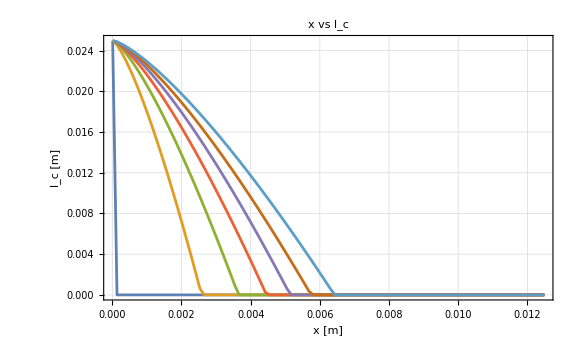
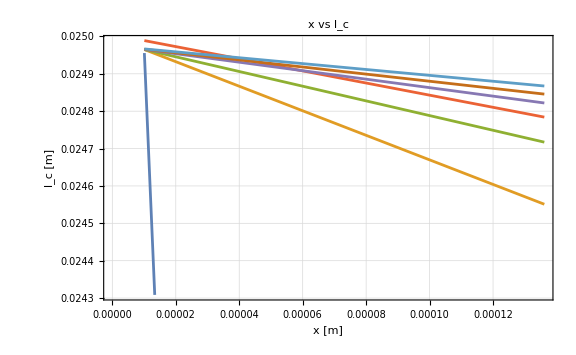

```mathematica
Row[{ListPlot[Evaluate@Table[Transpose[{xrange,lcnum[[i]]}],{i,1,Length@lcnum}],
Joined->True,ImageSize->Large,Evaluate@opts,FrameLabel->{"x [m]", "l_c [m]"},PlotLabel->"x vs l_c",ImageSize->Large],Spacer@2,ListPlot[Evaluate@Table[Transpose[{xrange[[1;;2]],lcnum[[i,1;;2]]}],{i,1,Length@lcnum}],Joined->True,ImageSize->Large,Evaluate@opts,FrameLabel->{"x [m]", "l_c [m]"},PlotLabel->"x vs l_c",ImageSize->Large]}]
```

#### Force

```mathematica
Ftmp=F/.Solve[eqxnoeps23,F][[1]]/.celldata//Simplify;
FxV[xx_,VV_]:=Ftmp/.{x->xx,V->VV}/.lc->lcxV[xx,VV]
```

```mathematica
Fnum=ParallelTable[FxV[xrange[[j]],Vrange[[i]]],{i,1,Length@Vrange},{j,1,Length@xrange}];
```

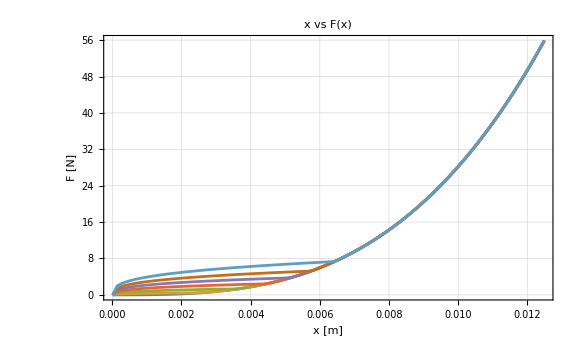
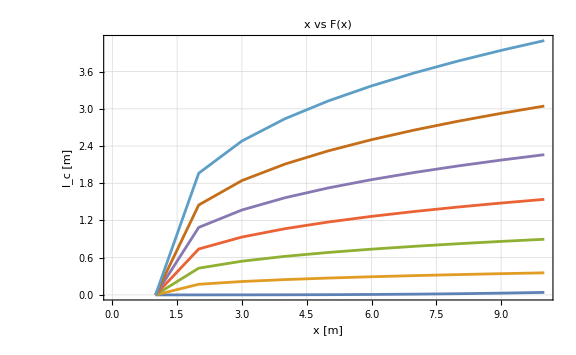

```mathematica
Row[{ListPlot[Evaluate@Table[Transpose[{xrange,Fnum[[i]]}],{i,1,Length@lcnum}]
,Joined->True,ImageSize->Large,Evaluate@opts,FrameLabel->{"x [m]", "F [N]"},PlotLabel->"x vs F(x)",ImageSize->Large],ListPlot[Fnum[[;;,1;;10]],Joined->True,ImageSize->Large,Evaluate@opts,FrameLabel->{"x [m]", "l_c [m]"},PlotLabel->"x vs F(x)",ImageSize->Large]}]
```

#### Capacitance

```mathematica
Ctmp=C1/.geometry/.zeroϵ2ϵ3/.celldata;
CxV[xx_,VV_]:=Ctmp/.{x->xx,V->VV}/.lc->lcxV[xx,VV]
```

```mathematica
Cnum=ParallelTable[CxV[xrange[[j]],Vrange[[i]]],{i,1,Length@Vrange},{j,1,Length@xrange}];
```

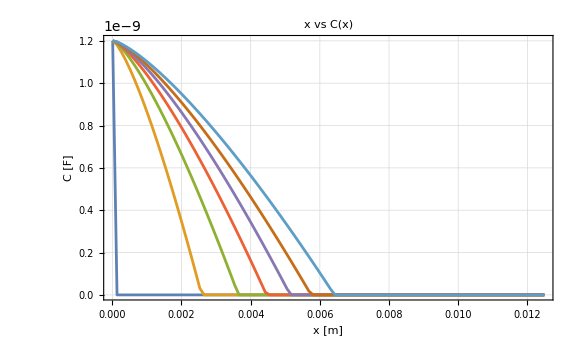
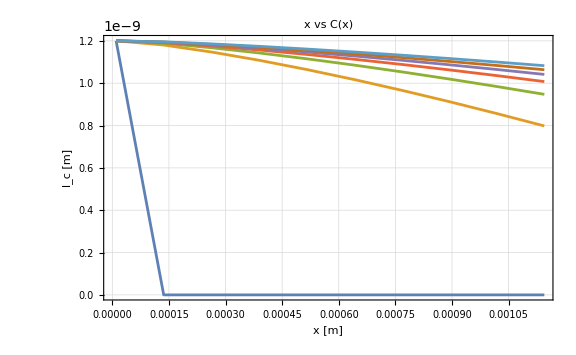

```mathematica
Row[{ListPlot[Table[Transpose[{xrange,Cnum[[i]]}],{i,1,Length@lcnum}],Joined->True,ImageSize->Large,Evaluate@opts,FrameLabel->{"x [m]", "C [F]"},PlotLabel->"x vs C(x)",ImageSize->Large],
ListPlot[Table[Transpose[{xrange[[1;;10]],Cnum[[i,1;;10]]}],{i,1,Length@lcnum}],Joined->True,ImageSize->Large,Evaluate@opts,FrameLabel->{"x [m]", "l_c [m]"},PlotLabel->"x vs C(x)",ImageSize->Large]}]
```

```mathematica
xmin=xminth
```

0.0000101

### l_0 variation

```mathematica
styles={Automatic,Dashed,DotDashed};
```

```mathematica
l0range=oneDOF["l0range"];
ξ0range=oneDOF["ξ0range"];
```

```mathematica
sollcxVl0=sollc/.l0->l00/.celldata/.l00->l0;
solFxVl0=F/.Solve[eqxnoeps23,F][[1]]/.lc->sollc/.l0->l00/.celldata/.l00->l0;
solC1xVl0=C1/.geometry/.zeroϵ2ϵ3/.lc->sollc/.l0->l00/.celldata/.l00->l0;
```

```mathematica
lcxVl0[xx_,VV_,l00_]:=Clip[sollcxVl0/.{x->xx,V->VV,l0->l00},{10^-7,l00/.celldata}]
FxVl0[xx_,VV_,l00_]:=solFxVl0/.{x->xx,V->VV,l0->l00}
C1xVl0[xx_,VV_,l00_]:=Clip[solC1xVl0/.{x->xx,V->VV,l0->l00},{10^-18,Infinity}]
```

```mathematica
lcl0=Table[ParallelTable[lcxVl0[xrange[[j]],Vrange[[i]],l0range[[k]]],{i,1,Length@Vrange},{j,1,Length@xrange}],{k,1,Length@l0range}];
Fl0=Table[ParallelTable[FxVl0[xrange[[j]],Vrange[[i]],l0range[[k]]],{i,1,Length@Vrange},{j,1,Length@xrange}],{k,1,Length@l0range}];
Cl0=Table[ParallelTable[C1xVl0[xrange[[j]],Vrange[[i]],l0range[[k]]],{i,1,Length@Vrange},{j,1,Length@xrange}],{k,1,Length@l0range}];
```

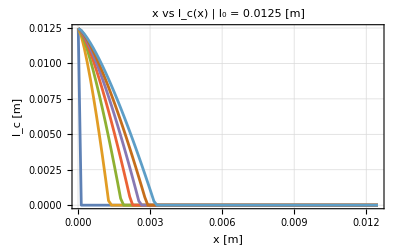
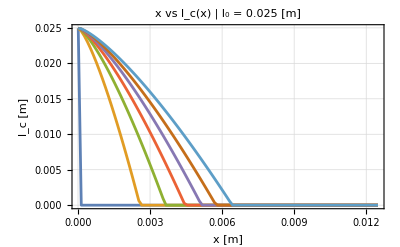
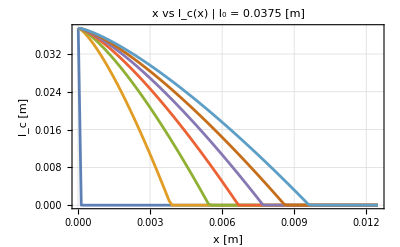

```mathematica
Row[
Table[ListPlot[Table[Transpose[{xrange,lcl0[[k,i]]}],{i,1,7}],Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "l_c [m]"},PlotLabel->StringJoin["x vs l_c(x) | l_0 = ",ToString[l0range[[k]]]," [m]"],PlotRange->All,ImageSize->400],{k,1,Length@l0range}]
]
```

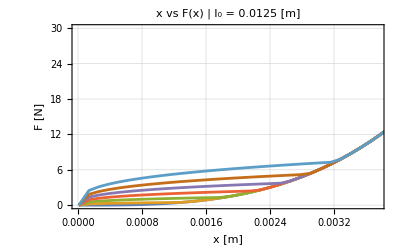
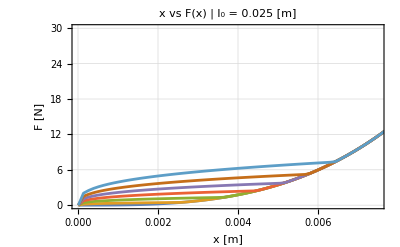
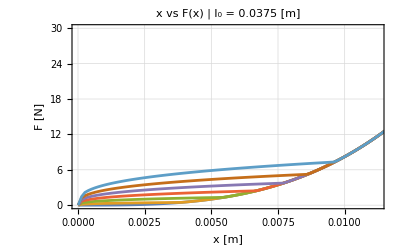

```mathematica
Row[
Table[ListPlot[Table[Transpose[{xrange,Fl0[[k,i]]}],{i,1,7}],Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "F [N]"},PlotLabel->StringJoin["x vs F(x) | l_0 = ",ToString[l0range[[k]]]," [m]"],PlotRange->{{Automatic,0.3 l0range[[k]]},{0,30}},ImageSize->400],{k,1,Length@l0range}]
]
```

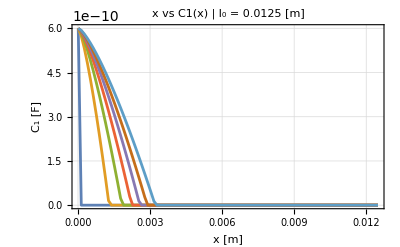
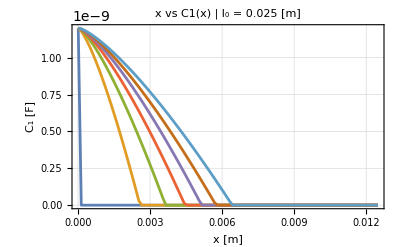
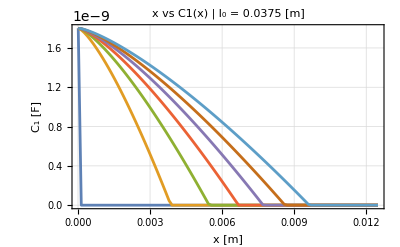

```mathematica
Row[
Table[ListPlot[Table[Transpose[{xrange,Cl0[[k,i]]}],{i,1,7}],Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "C_1 [F]"},PlotLabel->StringJoin["x vs C1(x) | l_0 = ",ToString[l0range[[k]]]," [m]"],PlotRange->All,ImageSize->400],{k,1,Length@l0range}]
]
```

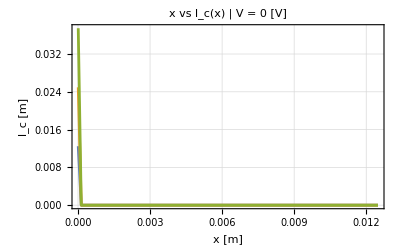
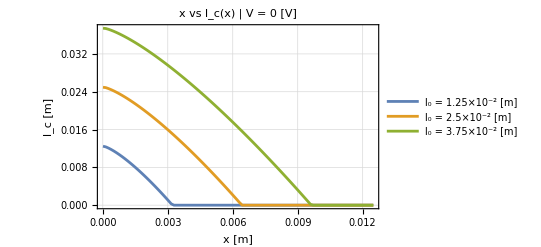

```mathematica
Row[{
ListPlot[Evaluate@Table[Transpose[{xrange,lcl0[[k,1]]}],{k,1,Length@l0range}],Joined->True,PlotStyle->colors,Evaluate@opts,
PlotRange->All,PlotLabel->"x vs l_c(x) | V = 0 [V]",FrameLabel->{"x [m]", "l_c [m]"},ImageSize->400],
ListPlot[Evaluate@Table[Transpose[{xrange,Last@lcl0[[k]]}],{k,1,Length@l0range}],Joined->True,PlotStyle->colors,Evaluate@opts,
PlotRange->All,PlotLabel->"x vs l_c(x) | V = 0 [V]",FrameLabel->{"x [m]", "l_c [m]"},ImageSize->400,PlotLegends->l0strings]
}]
```

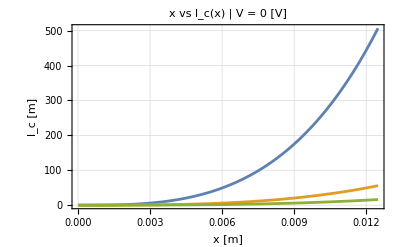
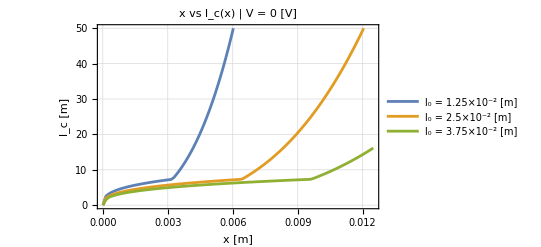

```mathematica
Row[{
ListPlot[Evaluate@Table[Transpose[{xrange,Fl0[[k,1]]}],{k,1,Length@l0range}],Joined->True,PlotStyle->colors,Evaluate@opts,
PlotRange->All,PlotLabel->"x vs l_c(x) | V = 0 [V]",FrameLabel->{"x [m]", "l_c [m]"},ImageSize->400],
ListPlot[Evaluate@Table[Transpose[{xrange,Last@Fl0[[k]]}],{k,1,Length@l0range}],
Joined->True,PlotStyle->colors,Evaluate@opts,PlotRange->{Automatic,{0,50}},PlotLabel->"x vs l_c(x) | V = 0 [V]",FrameLabel->{"x [m]", "l_c [m]"},ImageSize->400,PlotLegends->l0strings]
}]
```

### Elastic energy from x - F

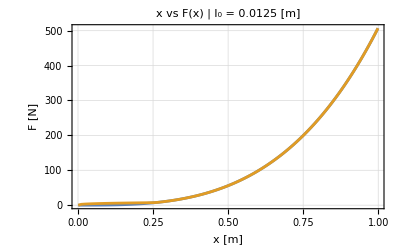
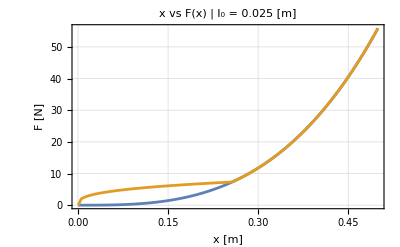
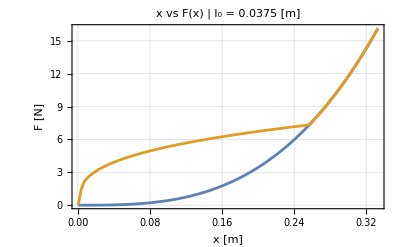

```mathematica
FintVmaxl0=Table[Interpolation[Transpose[{xrange,Last@Fl0[[i]]}]],{i,1,Length@l0range}];
FintVminl0=Table[Interpolation[Transpose[{xrange,Fl0[[i,1]]}]],{i,1,Length@l0range}];
Row[
Table[
ListPlot[Table[Transpose[{xrange/l0range[[k]],Fl0[[k,i]]}],{i,{1,Length@Vrange}}],Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "F [N]"},PlotLabel->StringJoin["x vs F(x) | l_0 = ",ToString[l0range[[k]]]," [m]"],PlotRange->All,ImageSize->400],{k,1,Length@l0range}]
]
```

```mathematica
xrangel0=Table[Array[#&,100,{xminth,0.5 l0range[[i]]}],{i,1,Length@l0range}];xrangel0//Length
xrangel0norm=xrangel0/l0range;
```

3

```mathematica
Uelxl0=Table[
ParallelTable[NIntegrate[FintVmaxl0[[i]][x]-FintVminl0[[i]][x],{x,xminth,xfin}],{xfin,xrangel0[[i,1]],Last@xrangel0[[i]],GetStep@xrangel0[[i]]}],{i,1,Length@l0range}];
```

```mathematica
Voltmpxlc=Vol/.geometry/.zeroϵ2ϵ3/.{l0->l0range,ξ0->ξ0range}/.celldata//Simplify;
Voll0=Table[Voltmpxlc[[i]]/.{x->xrangel0[[i]],lc->Last@lcl0[[i]]},{i,1,Length@l0range}];
uelxl0=Uelxl0/Voll0/.celldata;
```

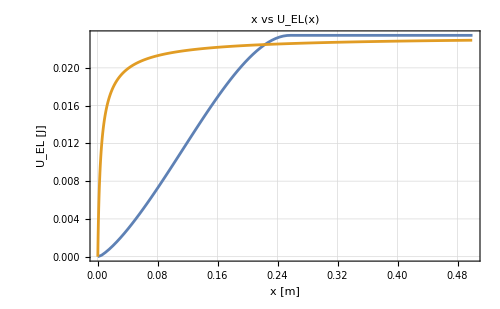
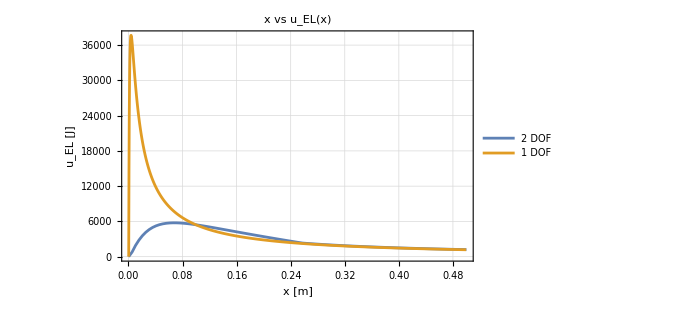

```mathematica
Row[{
ListPlot[{
Transpose[{xrangel0norm[[2]],Uelxl0[[2]]}],
Transpose[{Flatten@oneDOF["PSTRAIN","xrange"][[2]]/l0/.celldata,oneDOF["PSTRAIN","Uelx"]}]},
Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "U_EL [J]"},PlotLabel->"x vs U_EL(x)",PlotRange->All,ImageSize->500],
ListPlot[{
Transpose[{xrangel0norm[[2]],uelxl0[[2]]}],
Transpose[{Flatten@oneDOF["PSTRAIN","xrange"][[2]]/l0/.celldata,oneDOF["PSTRAIN","uelx"]}]},
Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "u_EL [J]"},PlotLegends->{"2 DOF","1 DOF"},PlotLabel->"x vs u_EL(x)",PlotRange->All,ImageSize->500]}]
```

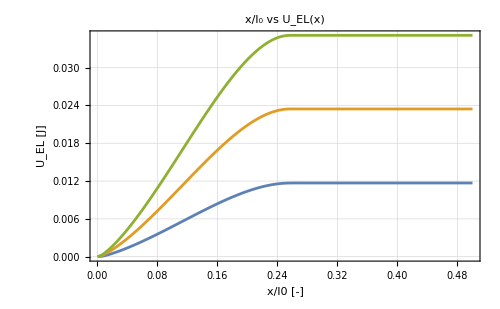
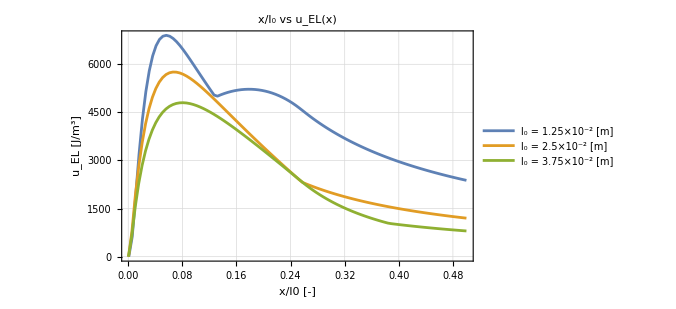

```mathematica
Row@{
Show[
ListPlot[Table[Transpose[{xrangel0norm[[i]],Uelxl0[[i]]}],{i,1,Length@l0range}],Joined->True],
Evaluate@opts,PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},PlotRange->All,ImageSize->500],Spacer@100,
Show[
ListPlot[Table[Transpose[{xrangel0norm[[i]],uelxl0[[i]]}],{i,1,Length@l0range}],Joined->True,PlotLegends->l0strings],
Evaluate@opts,PlotLabel->"x/l_0 vs u_EL(x)",FrameLabel->{"x/l0 [-]","u_EL [J/m^3]"}
,PlotRange->All,ImageSize->500]}
```

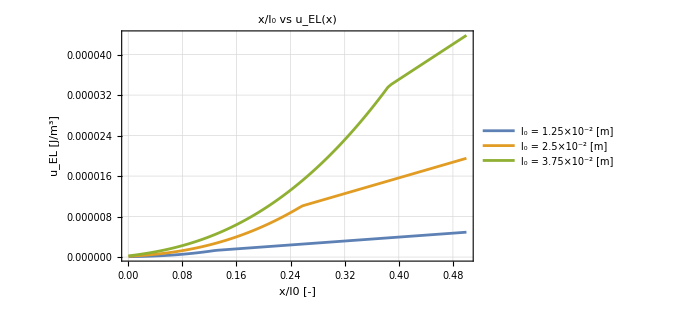

```mathematica
Show[
ListPlot[Table[Transpose[{xrangel0norm[[i]],Voll0[[i]]}],{i,1,Length@l0range}],Joined->True,PlotLegends->l0strings],
Evaluate@opts,PlotLabel->"x/l_0 vs u_EL(x)",FrameLabel->{"x/l0 [-]","u_EL [J/m^3]"}
,PlotRange->All,ImageSize->500]
```

### Q-V plot

Minimum strain -> C1 max, Maximum strain -> C1 min, C =Q/V, V  = Q/C, Q = C V

```mathematica
Cmax=C1/.geometry/.zeroϵ2ϵ3/.celldata/.lc->sollcxV/.x->xrange[[1]]/.V->Last@Vrange
Cmin=C1/.geometry/.zeroϵ2ϵ3/.celldata/.lc->sollcxV/.x->Last@xrange/.V->Last@Vrange
```

1.19981×10^-9

4.80728×10^-15

```mathematica
QminVmax=Q/.Solve[Q/Cmin==Last@Vrange][[1]]
QmaxVmax=Q/.Solve[Q/Cmax==Last@Vrange][[1]]
```

3.00441×10^-11

7.49845×10^-6

```mathematica
Vminstr[Q_]:=Piecewise[{{Q/Cmax, Between[Q,{0,QmaxVmax}]}, {-10^-50, Not@Between[Q,{0,QmaxVmax}]}}]
Vmaxstr[Q_]:=Piecewise[{{Q/Cmin, Between[Q,{0,QminVmax}]}, {-10^-50, Not@Between[Q,{0,QminVmax}]}}]
VmaxofQ[Q_]:=Piecewise[{{Interpolation[Transpose@{LinSpace[QminVmax,QmaxVmax,10],ConstantArray[Last@Vrange,10]}][Q], Between[Q,{QminVmax,QmaxVmax}]}, {-10^-50, Not@Between[Q,{QminVmax,QmaxVmax}]}}]
```

```mathematica
plQV[linestyle_]:=Show[
Plot[{Vminstr[Q],,VmaxofQ[Q]},{Q,0,QmaxVmax},PlotLegends->{"Min. strain","Max. strain","V_MAX"},PlotStyle->linestyle],
Plot[{Vmaxstr[Q]},{Q,0,QminVmax},PlotStyle->Union[{linestyle},{colors[[2]]}]],
PlotLabel->"Q vs V",FrameLabel->{"Q [A]","V [V]"},ImageSize->Large,PlotRange->{Automatic,{0,Automatic}},Evaluate@opts
];
```

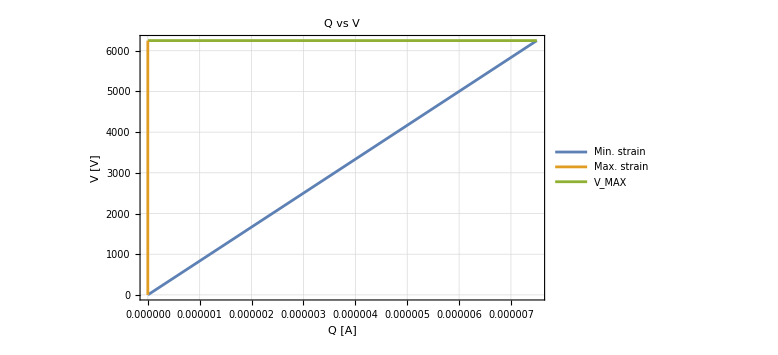

```mathematica
plQV[Automatic]
```

```mathematica
UelQV=ParallelTable[NIntegrate[Vmaxstr[Q]+VmaxofQ[Q]-Vminstr[Q],{Q,0,Qfin}],{Qfin,0,QmaxVmax,10^-7}];
```

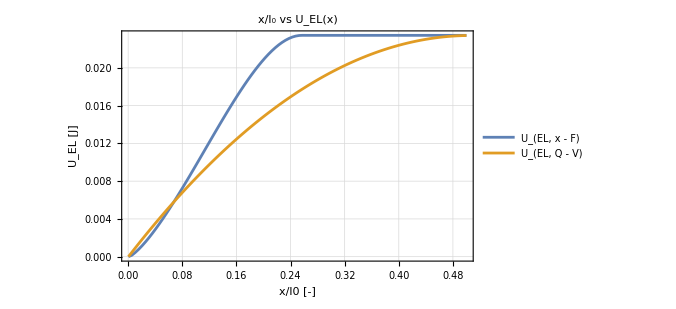

```mathematica
Show[
ListPlot[{Transpose[{xrangel0norm[[2]],Uelxl0[[2]]}],Transpose[{LinSpace[xrangel0norm[[2,1]],Last@xrangel0norm[[2]],Length@UelQV],UelQV}]},Joined->True,PlotLegends->{"U_(EL,  x - F)","U_(EL,  Q - V)"},Evaluate@opts],
PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},PlotRange->All,ImageSize->500]
```

### Energy plots in working conditions

```mathematica
FintV0=FintVminl0[[2]];
FintVmax=FintVmaxl0[[2]];
xintFV0=Interpolation[Transpose@{Fnum[[1]],xrange}];
xintFVmax=Interpolation[Transpose@{Last@Fnum,xrange}];
```

```mathematica
fixedFpath[n_,Flower_,Fupper_,xintFV0_,xintFVmax_,Vrange_]:=Module[{xA,xB,xC,xD,xrangeAB,xrangeBC,xrangeCD,xrangeDA,VAB,VBC,VCD,VDA,CAB,CBC,CCD,CDA,QAB,QBC,QCD,QDA},
xA=xintFV0[Flower];
xB=xintFVmax[Flower];
xC=xintFVmax[Fupper];
xD=xintFV0[Fupper];
xrangeAB=LinSpace[xA,xB,n];xrangeBC=LinSpace[xB,xC,n];xrangeCD=LinSpace[xC,xD,n];xrangeDA=LinSpace[xD,xA,n];
VAB=LinSpace[Vrange[[1]],Last@Vrange,n];VBC=ConstantArray[Last@Vrange,n];VCD=LinSpace[Last@Vrange,Vrange[[1]],n];VDA=ConstantArray[Vrange[[1]],n];
CAB=CxV[x,V]/. {x->xrangeAB,V->VAB};CBC=CxV[x,Last@Vrange]/. x->xrangeBC;CCD=CxV[x,V]/. {x->xrangeCD,V->VCD};CDA=CxV[x,Vrange[[1]]]/. x->xrangeDA;
VDA=ConstantArray[0,n];
QAB=CAB VAB;QBC=CBC VBC;QCD=CCD VCD;QDA=CDA VDA;
{{{xA,Flower},{xB,Flower},{xC,Fupper},{xD,Fupper}},{xrangeAB,xrangeBC,xrangeCD,xrangeDA},{VAB,VBC,VCD,VDA},{CAB,CBC,CCD,CDA},{QAB,QBC,QCD,QDA}}]
```

```mathematica
Block[{Flower=5,Fupper=7,n=3000},{
fixedF=fixedFpath[n,Flower,Fupper,xintFV0,xintFVmax,Vrange];
plfixedF=Show[
Plot[{FintV0[x],FintVmax[x]},{x,xminth,xmaxth},PlotRange->{{Automatic,0.008},{0,20}},PlotRange->All,ImageSize->Large],
Plot[FintV0[x],{x,fixedF[[1,1,1]],fixedF[[1,4,1]]},PlotStyle->Darker@Red],Plot[FintVmax[x],{x,fixedF[[1,2,1]],fixedF[[1,3,1]]},PlotStyle->Darker@Red],
Block[{ytol=0.6},Graphics[{Darker@Red,Thick,Line[{fixedF[[1,1]],fixedF[[1,2]]}],Line[{fixedF[[1,3]],fixedF[[1,4]]}],
MapThread[Text[Style[#1,Bold],#2+{0,-ytol}]&,{{"A","B","C","D"},fixedF[[1,1;;4]]}]
}]]
,Evaluate@opts,FrameLabel->{"x [m]", "F [N]"},PlotLabel->"Fixed force",PlotRange->All];
}];
```

### Fixed force

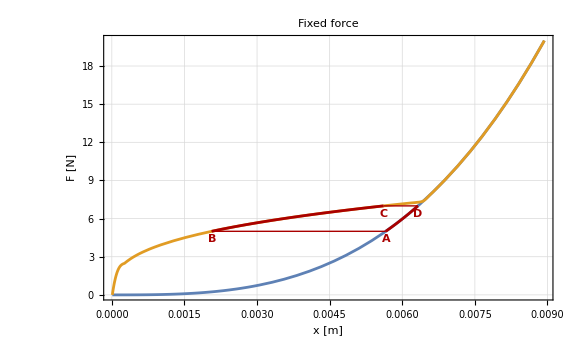
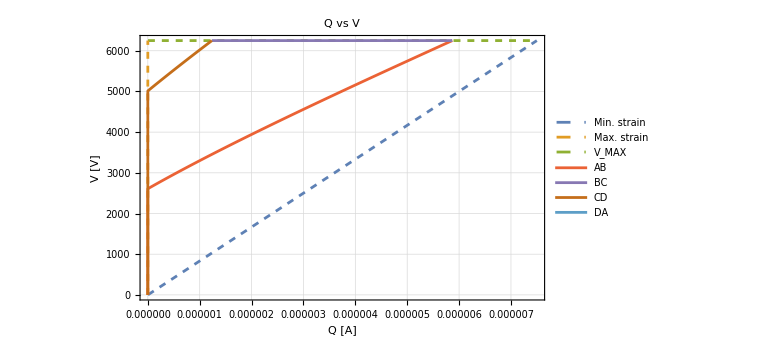

```mathematica
Row[{
plfixedF,
Show[plQV[Dashed],
ListPlot[Table[Transpose[{fixedF[[5,i]],fixedF[[3,i]]}],{i,1,Length@fixedF[[5]]}],PlotStyle->colors[[4;;7]],
Joined->True,Evaluate@opts,FrameLabel->{"Q [A]", "V [V]"},PlotLabel->"Q - V",PlotLegends->{"AB","BC","CD","DA"},ImageSize->Large]]
}]
```

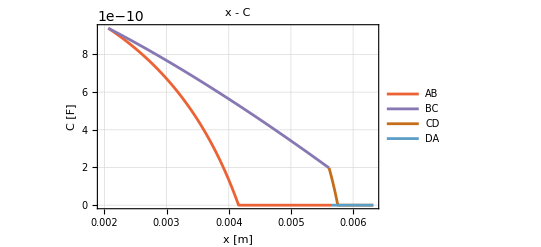

```mathematica
ListPlot[Table[Transpose[{fixedF[[2,i]],fixedF[[4,i]]}],{i,1,Length@fixedF[[2]]}],PlotStyle->colors[[4;;7]],
Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "C [F]"},PlotLabel->"x - C",PlotLegends->{"AB","BC","CD","DA"}]
```

#### Check area of regions

```mathematica
Integrate[FintVmax[x],{x,fixedF[[1,2,1]],fixedF[[1,3,1]]}]+fixedF[[1,3,2]](fixedF[[1,4,1]]-fixedF[[1,3,1]])-(fixedF[[1,1,1]]-fixedF[[1,2,1]])fixedF[[1,2,2]]-Integrate[FintV0[x],{x,fixedF[[1,1,1]],fixedF[[1,4,1]]}]
```

0.00471845

```mathematica
Table[Integrate[
Interpolation[Transpose[{Sort[Last[fixedF][[k]]],Sort[fixedF[[3,k]]]}],InterpolationOrder->1][Q],
{Q,Sort[Last[fixedF][[k]]][[1]],Last@Sort[Last[fixedF][[k]]]}],{k,1,4}]
%[[3]]+%[[2]]-%[[1]]
```

Interpolation::inddp: The point 0. in dimension 1 is duplicated.

{0.0263581,0.0289551,0.00696702,0}

0.009564

### Fixed x

```mathematica
fixedxpath[n_,xrightlower_,xleftlower_,FintV0_,FintVmax_,Vrange_]:=Module[{xA,xB,xC,xD,xrangeAB,xrangeBC,xrangeCD,xrangeDA,VAB,VBC,VCD,VDA,CAB,CBC,CCD,CDA,QAB,QBC,QCD,QDA},
xA=xrightlower;
xB=xleftlower;
xC=xB;
xD=xA;
xrangeAB=LinSpace[xA,xB,n];xrangeBC=ConstantArray[xB,n];xrangeCD=LinSpace[xC,xD,n];xrangeDA=ConstantArray[xA,n];
VAB=ConstantArray[Vrange[[1]],n];VBC=LinSpace[Vrange[[1]],Last@Vrange,n];VCD=ConstantArray[Last@Vrange,n];VDA=LinSpace[Last@Vrange,Vrange[[1]],n];
CAB=CxV[x,V]/. {x->xrangeAB,V->VAB};CBC=CxV[x,V]/. {x->xrangeBC,V->VBC};CCD=CxV[x,V]/. {x->xrangeCD,V->VCD};CDA=CxV[x,V]/. {x->xrangeDA,V->VDA};
VAB=ConstantArray[0,n];
QAB=CAB VAB;QBC=CBC VBC;QCD=CCD VCD;QDA=CDA VDA;
{{{xA,FintV0[xA]},{xB,FintV0[xB]},{xC,FintVmax[xC]},{xD,FintVmax[xD]}},{xrangeAB,xrangeBC,xrangeCD,xrangeDA},{VAB,VBC,VCD,VDA},{CAB,CBC,CCD,CDA},{QAB,QBC,QCD,QDA}}]
```

```mathematica
Block[{xrightlower=0.005,xleftlower=0.003,n=1000},{
fixedx=fixedxpath[n,xrightlower,xleftlower,FintV0,FintVmax,Vrange];
plfixedx=Show[
Plot[{FintV0[x],FintVmax[x]},{x,xminth,xmaxth},PlotRange->{{Automatic,0.008},{0,20}},Evaluate@opts,FrameLabel->{"x [m]", "F [N]"},PlotRange->All,ImageSize->Large],
Block[{xtol=0.00015,ytol=0.4,A=fixedx[[1,1]],B=fixedx[[1,2]],CC=fixedx[[1,3]],DD=fixedx[[1,4]]},{
Plot[FintV0[x],{x,A[[1]],B[[1]]},PlotStyle->Darker@Red],Plot[FintVmax[x],{x,CC[[1]],DD[[1]]},PlotStyle->Darker@Red],
Graphics[{Darker@Red,Thick,Line[{A,DD}],Line[{B,CC}],
MapThread[Text[Style[#1,Bold],#2+{xtol,-ytol}]&,{{"A","B","C","D"},fixedx[[1,1;;4]]}]
}]
}]
,Evaluate@opts,FrameLabel->{"x [m]", "F [N]"},PlotLabel->"Fixed x"];
}];
```

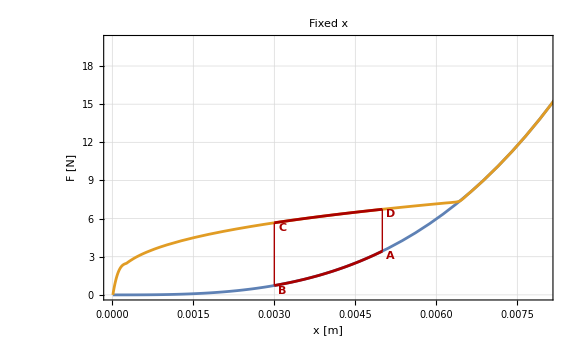
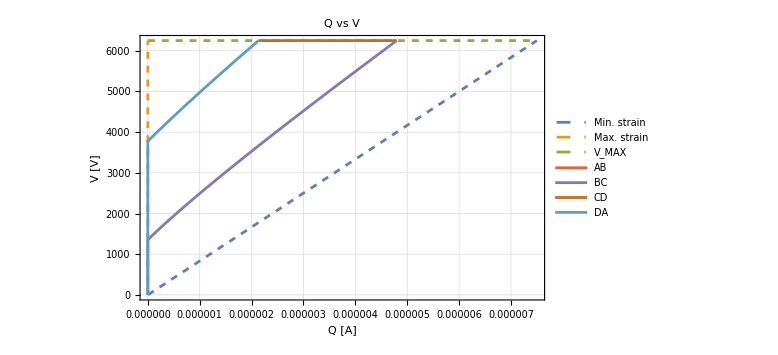

```mathematica
Row[{
plfixedx,
Show[plQV[Dashed],
ListPlot[Table[Transpose[{fixedx[[5,i]],fixedx[[3,i]]}],{i,1,Length@fixedx[[5]]}],PlotStyle->colors[[4;;7]],
Joined->True,Evaluate@opts,FrameLabel->{"Q [A]", "V [V]"},PlotLabel->"Q - V",PlotLegends->{"AB","BC","CD","DA"},ImageSize->Large]]
}]
```

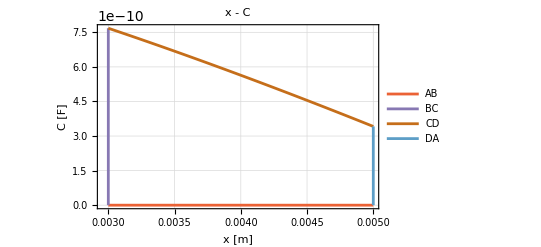

```mathematica
ListPlot[Table[Transpose[{fixedx[[2,i]],fixedx[[4,i]]}],{i,1,Length@fixedx[[2]]}],PlotStyle->colors[[4;;7]],
Joined->True,Evaluate@opts,FrameLabel->{"x [m]", "C [F]"},PlotLabel->"x - C",PlotLegends->{"AB","BC","CD","DA"}]
```

#### Check area of regions

```mathematica
NIntegrate[FintVmax[x]-FintV0[x],{x,fixedx[[1,2,1]],fixedx[[1,1,1]]}]
```

0.00873363

```mathematica
Table[Integrate[
Interpolation[Transpose[{Sort[Last[fixedx][[k]]],Sort[fixedx[[3,k]]]}],InterpolationOrder->1][Q],
{Q,Sort[Last[fixedx][[k]]][[1]],Last@Sort[Last[fixedx][[k]]]}],{k,1,4}]
%[[4]]+%[[3]]-%[[2]]
```

Interpolation::inddp: The point 0. in dimension 1 is duplicated.

{0,0.0186717,0.0166424,0.0107629}

0.00873363